## LLMs - What has changed?

Marco Thiel
office: Meston Building 332
m.thiel@abdn.ac.uk
Tel: 01224 27 3160

Thursday 22 September, 2025

## How important is programming for data science?

Suppose all the skills you need to do data science add up to 100. How much (how important) is programming out of that?

```mathematica
(*CreateDatabin["ClassMScDataScience2024"]*)
```

```mathematica
importanceProgramming=Databin["1py8yOGbe"];
```

```mathematica
CloudDeploy[FormFunction[FormObject[{"programming","How important are programming skills for data science (1-100)?"}-><|"Interpreter"->Restricted["Number",{1,100}],"Control"->Slider|>],(DatabinAdd[importanceProgramming,<|"programming"->#programming|>];Style["Thank You!", Large])&,AppearanceRules->{"Title"-> "Poll: How important is programming for data science?\n","Description"->"Suppose all the skills you need to do data science add up to 100. How much (how important) is programming out of that?\n\n"}],CloudObject["https://www.wolframcloud.com/obj/39bb4c01-dad0-4113-b7a9-5b8be7dd06e0"],Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/39bb4c01-dad0-4113-b7a9-5b8be7dd06e0]

```mathematica
ImageResize[BarcodeImage["https://www.wolframcloud.com/obj/39bb4c01-dad0-4113-b7a9-5b8be7dd06e0","QR"],400]
```

-Graphics-

### Results of the poll

```mathematica
Histogram["programming"/.("Data"/.Get@Databin["1py8yOGbe"]),PlotRange->{{0,100},All},PlotTheme->"Marketing",AxesLabel->{"level of importance","number of votes"},PlotLabel->"Importance of programming for Data Science",LabelStyle->Directive[ Bold,20],ImageSize->Large]
```

## Skills for Data Science

Technical Skills Required For Data Scientists (https://www.simplilearn.com/what-skills-do-i-need-to-become-a-data-scientist-article#skills_required_for_data_scientists)

Some of the most important technical data scientist skills are:
	•	Statistical analysis and computing
	•	Machine Learning
	•	Deep Learning
	•	Processing large data sets
	•	Data Visualization
	•	Data Wrangling
	•	Mathematics
	•	Programming
	•	Statistics
	•	Big Data

1. Programming
You need to have knowledge of various programming languages, such as Python, Perl, C/C++, SQL, and Java, with Python being the most common coding language required in data science roles. These programming languages help data scientists organize unstructured data sets.

2. Knowledge of SAS and Other Analytical Tools
Understanding analytical tools is one of the most helpful data scientist skills for extracting valuable information from an organized data set. SAS, Hadoop, Spark, Hive, Pig, and R are the most popular data analytical tools that data scientists use. 

3. Adept at Working with Unstructured Data
Data scientists should have experience working with unstructured data that comes from different channels and sources. For example, if a data scientist is working on a  project to help the marketing team provide insightful research, the professional should be well adept at handling social media as well.
Some of the other data scientist skills required are Machine Learning, Artificial intelligence, Deep learning, Probability and Statistics.

4. Web Scraping
Web scraping is the automated process of extracting data from webpages.

5. ML with AI and DL with NLP:
Deep learning (DL) with natural language processing (NLP) focuses on using neural networks to process and understand human language. Machine learning (ML) and artificial intelligence (AI) are both concerned with teaching computers to learn from data.

6. Problem-Solving Skills:
Skills for Solving Issues the capacity to evaluate challenging issues and develop workable answers.

7. Probability and Statistics:
Statistics and probability is the study of randomness and uncertainty in statistics, and the application of mathematical tools to decision-making.

8. Multivariate Calculus and Linear Algebra:
Advanced mathematical ideas used in machine learning and data analysis include multivariate calculus and linear algebra.

9. Database Management:
The procedure of arranging, saving, and accessing data in a database system is known as database management.

10. Cloud Computing:
Utilizing remote servers to store, control, and handle data and applications online is known as cloud computing.

11. Microsoft Excel:
Microsoft Excel is a spreadsheet program used for data display and analysis.

12. DevOps:
A technique of developing software that places a strong emphasis on teamwork and communication between the development and operations teams.

13. Data Extraction, Transformation, and Loading:
Data collection, cleansing, and preparation for analysis is known as data extraction, transformation, and loading.

14. Business Intelligence:
Business intelligence is the process of using tools and techniques for data analysis to acquire knowledge and guide business decisions.

15. Neural Networks:
A data scientist should possess skills in designing, training, and fine-tuning neural networks for various use cases, as well as knowledge of different neural network architectures and frameworks.

16. Model Deployment:
Data scientists need expertise in model deployment, which involves making trained machine-learning models available for use in production environments.

17. Data Structures and Algorithms:
The fundamental ideas in computer science that underpin effective data storage, retrieval, and computational problems are known as data structures and algorithms.

### Non-technical skills required for data scientists

18. A Strong Business Acumen
The best way to productively channel technical skills is to have strong business acumen. Without it, an aspiring data scientist may not be able to discern the problems and potential challenges that need to be solved in order for an organization to grow. This is essential for helping the organization you’re working for explore new business opportunities.

19. Strong Communication Skills
Next on the list of top data scientist skills is communication. Data scientists clearly understand how to extract, understand, and analyze data. However, for you to be successful in your role, and for your organization to benefit from your services, you should be able to successfully communicate your findings with team members who don’t have the same professional background as you.  
	
20. Great Data Intuition
This is perhaps one of the most significant non-technical data scientist skills. Valuable data insights are not always apparent in large data sets, and a knowledgeable data scientist has intuition and knows when to look beyond the surface for insightful information. This makes data scientists more efficient in their work, and gaining this skill comes from experience and the right training. However, this data scientist skill comes with experience and bootcamps are a great way of polishing it.  

21. Analytical Mindset:
The capacity to dissect complicated issues into their component parts, analyze those parts, and derive conclusions from the data.

22. “Out-of-the-Box” Thinking:
Using creative and innovative thinking to generate novel ideas and unconventional answers.

23. Critical Thinking:
The process of evaluating and analyzing data in order to make a judgment or choice is known as critical thinking.

24. Decision Making:
Making decisions entails choosing the best course of action from a range of alternatives after carefully weighing all pertinent information.

## Stochastic vs Symbolic AI

## What are LLMs?

This is a text cell.

#### Generation of text based on n-grams - purely statistical

```mathematica
text=ExampleData[{"Text","AliceInWonderland"}];
```

```mathematica
newletter[s_,n_]:=If[Select[Normal[CharacterCounts[text,n+1]],StringTake[#[[1]],n]==StringTake[s,-n]&]=={},RandomChoice[Characters[text]],StringTake[RandomChoice[#[[All,2]]->#[[All,1]]&@Select[Normal[CharacterCounts[text,n+1]],StringTake[#[[1]],n]==StringTake[s,-n]&]],-1]]
```

```mathematica
Nest[StringJoin[#,newletter[#,2]]&,"I-",20]
```

I--ards ner, off, is b

```mathematica
Monitor[Table[<|k->Nest[StringJoin[#,newletter[#,k]]&,StringTake["Good morning class!",k],40]|>,{k,1,10}],k]
```

{<|1→G gogouthey alounutined ber the arbied on|>,<|2→Gookeplats, "an as evininning ons. "Con! O|>,<|3→Good me time upon a tree. The Caterpillarge|>,<|4→Good-by, feet and she who was a Hatter, what|>,<|5→Good   inakkcu asai"nf  aanuchs.w eoDg nhi nt|>,<|6→Good mye te orill di dhn'w tA nc hla nPt eirnf|>,<|7→Good moa'howkeftti-eo  "h  w nrakrcw "dse hohto|>,<|8→Good mormeolipshe.nmndaspdgr.mor rd r acdct ese |>,<|9→Good morn,av,abeifettr  se-u   sego siiuho "aehne|>,<|10→Good mornias sre_tvn es, ar Y t oenh vr  eapA m e |>}

```mathematica
Dataset[%]
```

### Let’s try this with GPT-2

```mathematica
ResourceSearch["GPT-2"]
```

```mathematica
lm=NetModel[{"GPT2 Transformer Trained on WebText Data","Task"->"LanguageModeling"}];
generateSample[languagemodel_][input_String,numTokens_:10,temperature_:1]:=Nest[Function[StringJoin[#,languagemodel[#,{"RandomSample","Temperature"->temperature}]]],input,numTokens];
```

```mathematica
Monitor[sentences=Table[<|k->generateSample[lm][StringTake["Good morning class",k],k,1]|>,{k,1,10}],k]
```

{<|1→G,|>,<|2→GoDF2018|>,<|3→GooGo_H|>,<|4→Good bio: A minor|>,<|5→Good _______ _____? |>,<|6→Good mb saLogon Senior Pros|>,<|7→Good moogle/mage crafting.- Name changes|>,<|8→Good morons in April when they said that burst|>,<|9→Good mornin' for ordinary mechanisms." Mr Hyde pointed|>,<|10→Good morni at the end." CSR-Honorary|>}

```mathematica
Dataset[sentences]
```

```mathematica
Monitor[sentences2=Table[<|k->generateSample[lm]["Good morning class",k,1]|>,{k,1,10}],k]
```

{<|1→Good morning class.|>,<|2→Good morning class when I|>,<|3→Good morning class," George says|>,<|4→Good morning class 1 geniuses,|>,<|5→Good morning class. Marco. It's|>,<|6→Good morning class. I've seen the announcements|>,<|7→Good morning class could hardly be anything more elegant than|>,<|8→Good morning class.


Would you like some|>,<|9→Good morning class," he asks Bill, offering.

|>,<|10→Good morning class. My question is this: Who's your greatest|>}

```mathematica
Dataset[sentences2]
```

```mathematica
generateSample[lm]["Albert Einstein was a German-born theoretical physicist",60]
```

Albert Einstein was a German-born theoretical physicist who was also known as Georg Laszlo von Peltier but a veteran of the Cold War. Laszlo later became Frank Ritter's assistant in the Office of Archivists of Germany during World War II.


Slide from page 2, history of Göring

### Let’s try that on GPT-3.5

```mathematica
LLMSynthesize["Albert Einstein was a German-born theoretical physicist "]
```

who is best known for his theory of relativity and his contributions to quantum mechanics. Born in Ulm, Germany in 1879, Einstein's early education was largely influenced by his interest in mathematics and physics. He eventually attended the Swiss Federal Polytechnic in Zurich, where he graduated in 1900.

After completing his studies, Einstein worked as a patent examiner at the Swiss Patent Office in Bern, during which time he published several groundbreaking papers in theoretical physics. In 1905, he published his renowned theory of relativity, which introduced the famous equation E=mc.b2 and laid the foundation for modern physics.

Throughout his career, Einstein made numerous contributions to the field of physics, including the theory of brownian motion, quantum theory of light, and the theory of general relativity. His work revolutionized our understanding of the fundamental laws of the physical world and had a profound impact on subsequent scientific research.

In 1921, Einstein was awarded the Nobel Prize in Physics for his discovery of the law of the photoelectric effect, which further supported the quantum theory of light. However, his most famous equation, E=mc.b2, is perhaps his most well-known contribution to science and is widely recognized as one of the most important and revolutionary equations in physics.

In addition to his scientific achievements, Einstein was also known for his humanitarian and social activism. He was a vocal advocate for civil rights, pacifism, and the formation of the United Nations. As a Jewish scientist, he experienced firsthand the rise of anti-Semitism in Germany and eventually emigrated to the United States in 1933, where he continued his scientific work at the Institute for Advanced Study in Princeton, New Jersey.

Albert Einstein passed away on April 18, 1955, but his legacy as one of the greatest physicists of all time continues to inspire and shape scientific progress to this day.

```mathematica
netGPT2=NetModel["GPT2 Transformer Trained on WebText Data"]
```

NetChain[<2>]

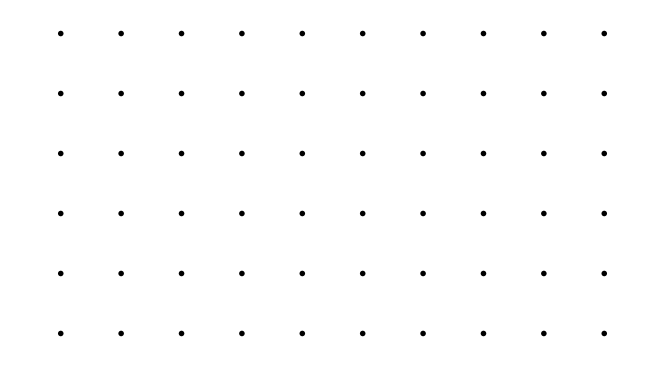

```mathematica
GraphicsGrid[Partition[Image/@Take[NetModel["Wolfram ImageIdentify Net V1"],1][-Graphics-],10]]
```

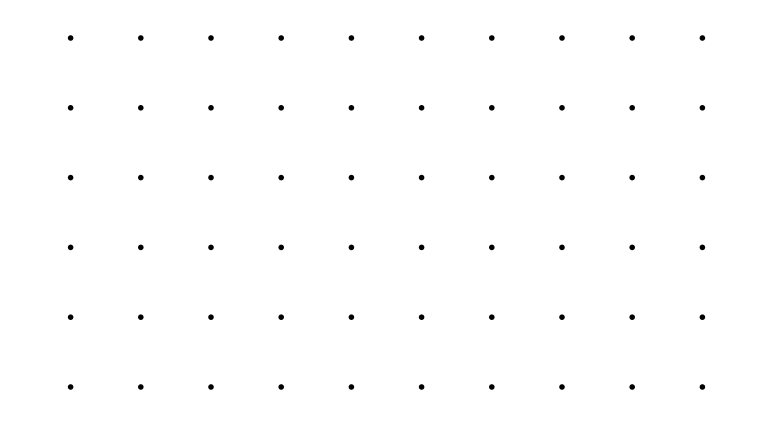

```mathematica
GraphicsGrid[Partition[Image[#,ImageSize->Medium]&/@Take[NetModel["Wolfram ImageIdentify Net V1"],1][-Graphics-],10],ImageSize->Large]
```

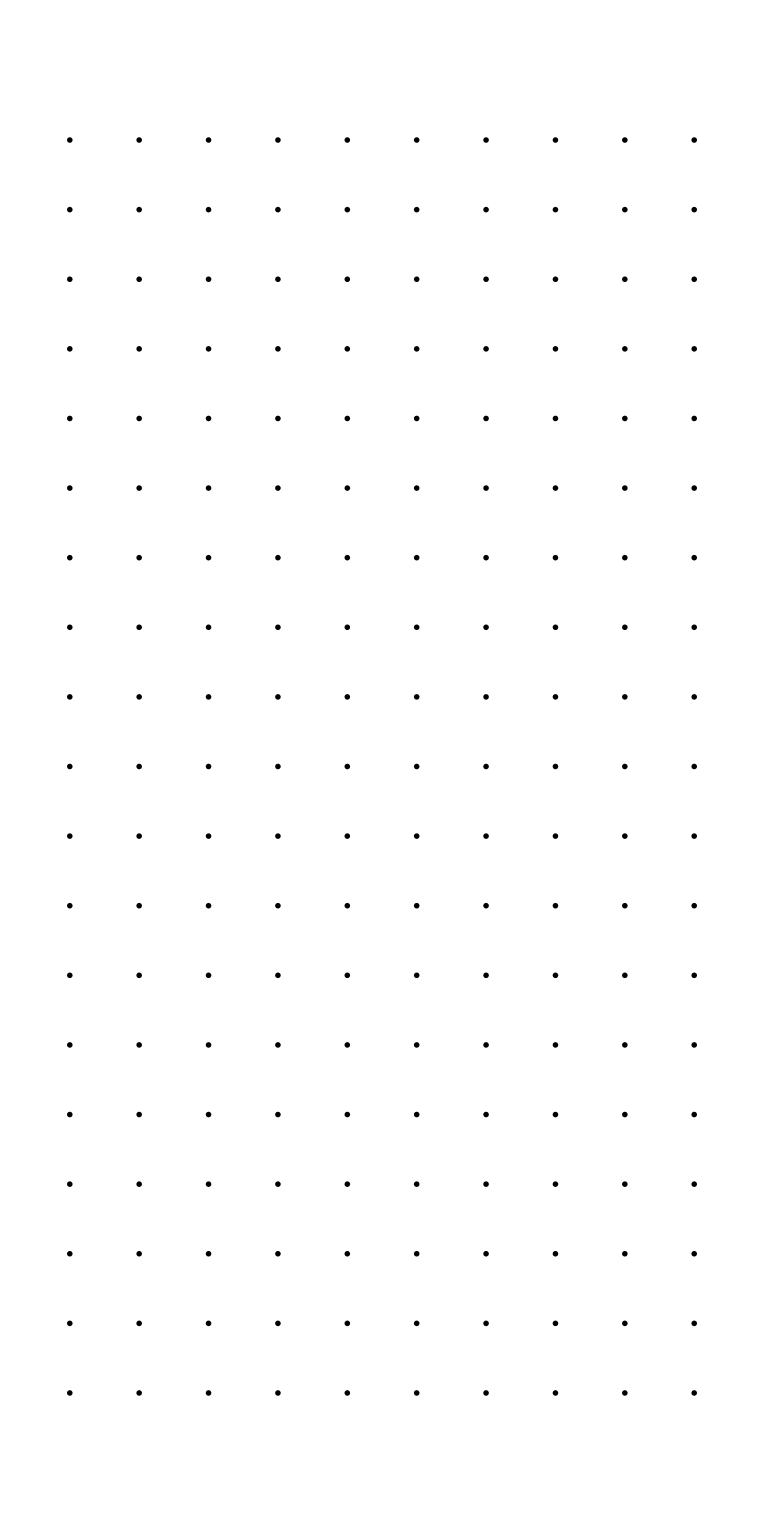

```mathematica
GraphicsGrid[Partition[Image[#,ImageSize->Medium]&/@Take[NetModel["Wolfram ImageIdentify Net V1"],10][-Graphics-],10],ImageSize->Large]
```

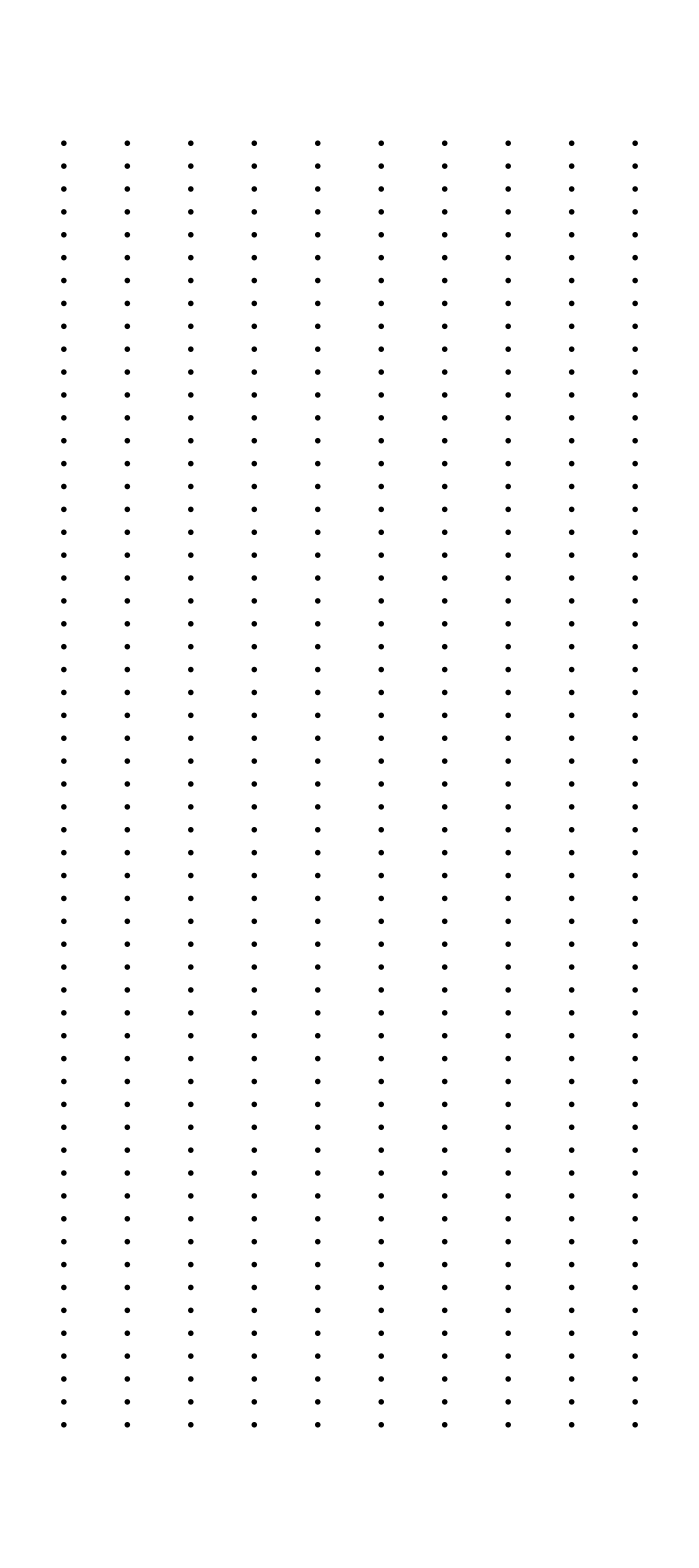

```mathematica
GraphicsGrid[Partition[Image[#,ImageSize->Medium]&/@Take[NetModel["Wolfram ImageIdentify Net V1"],15][-Graphics-],10],ImageSize->Large]
```

## Fitting

-Graphics-

## What is the assumption?

```mathematica
GraphicsRow[{-Graphics-,-Graphics-,-Graphics-},ImageSize->Full]
```

-Graphics-

## Chat GPT vs Wolfram Alpha

Earlier version of ChatGPT *January 2023*

Wolfram Alpha

Earlier ChatGPT

Wolfram Alpha

ChatGPT

Wolfram Alpha

-Graphics-

## Curve Fitting

```mathematica
data={{412.37109375,294.01953125},{364.3359375,414.13671875},{394.2265625,353.8828125},{448.49609375,353.38671875},{439.58203125,324.4609375},{435.48046875,303.75390625},{456.23828125,293.62890625},{428.30078125,263.8359375},{364.3671875,243.44921875},{370.65234375,221.41015625},{364.84375,192.69921875},{429.56640625,192.0390625},{421.4765625,32.53125},{300.35546875,78.76953125},{315.75,163.65625},{339.1875,226.87890625},{230.59375,91.96875},{215.30078125,99.1640625},{212.1015625,129.984375},{226.33203125,115.71875},{261.3203125,70.72265625},{92.03515625,98.8125},{115.23046875,83.0625},{134.01171875,116.1640625},{145.53125,134.1640625},{124.22265625,132.52734375},{185.5078125,163.265625},{194.8125,229.078125},{103.4296875,291.49609375},{85.43359375,188.45703125},{43.7734375,71.03125}};
```

## Fitting a straight line

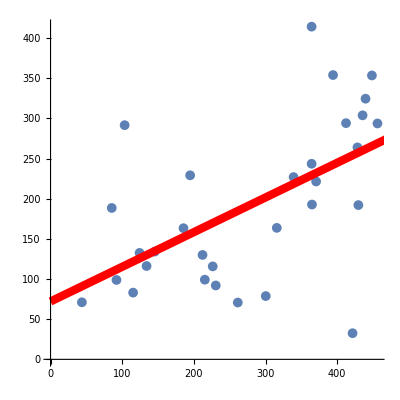

```mathematica
lm=FindFit[data,m x+b,{m,b},x];
Show[ListPlot[data,AspectRatio->1,Ticks->None,PlotMarkers->{Automatic,Medium}],Plot[m x+b/.lm,{x,0,1000},PlotStyle->Directive[Red,Thickness[0.015]]]]
```

## Fitting a parabola

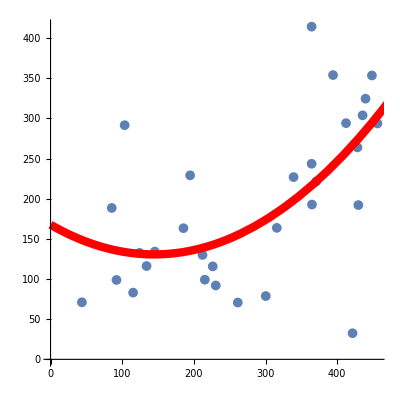

```mathematica
lm2=LinearModelFit[data,{x^2,x,1},x];Show[ListPlot[data,AspectRatio->1,Ticks->None,PlotMarkers->{Automatic,Medium}],Plot[lm2//Normal,{x,0,1000},PlotStyle->Directive[Red,Thickness[0.015]]]]
```

## Fitting a logarithm

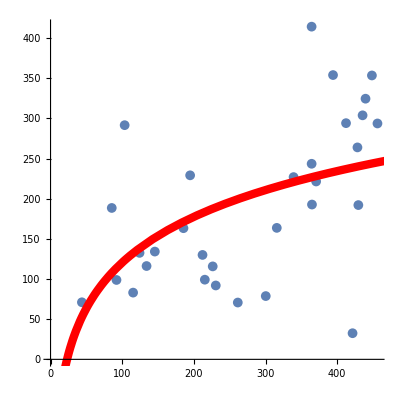

```mathematica
lm3=LinearModelFit[data,{Log[x],1},x];Show[ListPlot[data,AspectRatio->1,Ticks->None,PlotMarkers->{Automatic,Medium}],Plot[lm3//Normal,{x,0,1000},PlotStyle->Directive[Red,Thickness[0.015]]]]
```

## Interpolation

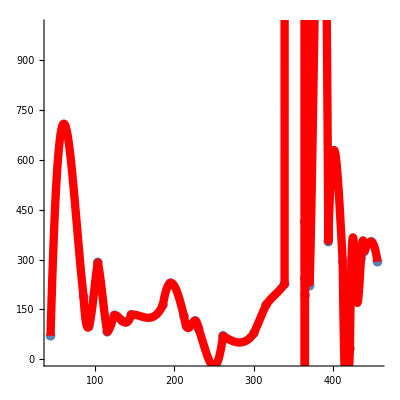

```mathematica
lmint=Interpolation[data,x,InterpolationOrder->3];Show[ListPlot[data,AspectRatio->1,Ticks->None,PlotMarkers->{Automatic,Medium}],Plot[lmint,{x,43.7734375,456.23828125},PlotStyle->Directive[Red,Thickness[0.015]]],PlotRange->{All,{0,1000}}]
```

## Can an LLM help?

There is an Example dataset on car stopping distances in Mathematica:

```mathematica
dataCar=ExampleData[{"Statistics","CarStoppingDistances"}]
```

{{4,2},{4,10},{7,4},{7,22},{8,16},{9,10},{10,18},{10,26},{10,34},{11,17},{11,28},{12,14},{12,20},{12,24},{12,28},{13,26},{13,34},{13,34},{13,46},{14,26},{14,36},{14,60},{14,80},{15,20},{15,26},{15,54},{16,32},{16,40},{17,32},{17,40},{17,50},{18,42},{18,56},{18,76},{18,84},{19,36},{19,46},{19,68},{20,32},{20,48},{20,52},{20,56},{20,64},{22,66},{23,54},{24,70},{24,92},{24,93},{24,120},{25,85}}

```mathematica
ExampleData[{"Statistics","CarStoppingDistances"},"LongDescription"]
```

Data on the relation between the speed of the car and the distance for the car to stop.

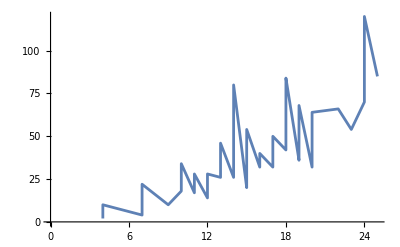

```mathematica
ListLinePlot[dataCar]
```

```mathematica
LLMFunction["Sbow Mathematica code to fit a linear model to the data `1`"][dataCar]
```

Here is the Mathematica code to fit a linear model to the given data:

```mathematica
data = {{4, 2}, {4, 10}, {7, 4}, {7, 22}, {8, 16}, {9, 10}, {10, 18}, {10, 26}, {10, 34}, {11, 17}, {11, 28}, {12, 14}, {12, 20}, {12, 24}, {12, 28}, {13, 26}, {13, 34}, {13, 34}, {13, 46}, {14, 26}, {14, 36}, {14, 60}, {14, 80}, {15, 20}, {15, 26}, {15, 54}, {16, 32}, {16, 40}, {17, 32}, {17, 40}, {17, 50}, {18, 42}, {18, 56}, {18, 76}, {18, 84}, {19, 36}, {19, 46}, {19, 68}, {20, 32}, {20, 48}, {20, 52}, {20, 56}, {20, 64}, {22, 66}, {23, 54}, {24, 70}, {24, 92}, {24, 93}, {24, 120}, {25, 85}};

lm = LinearModelFit[data, {1, x}, x];

lm["BestFitParameters"]
```

The output will be the best fit parameters for the linear model.

Let’s execute that fit:

```mathematica
lm = LinearModelFit[dataCar, {1, x}, x];
```

```mathematica
lm["BestFitParameters"]
```

{-17.5791,3.93241}

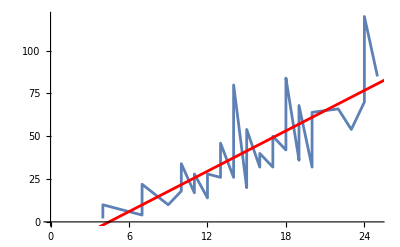

```mathematica
Show[ListLinePlot[dataCar],Plot[lm[x],{x,0,26},PlotStyle->Red]]
```

Is it reasonable to fit a linear model?

```mathematica
LLMSynthesize["Given a dataset that has speeds vs stopping distances of cars, what would be an approprite model to fit and why?"]
```

A common model that can be used to fit the given dataset of speeds vs stopping distances is a simple linear regression model. The linear regression model assumes a linear relationship between the predictor variable (speeds) and the response variable (stopping distances).

Linear regression is suitable in this case because it allows us to understand and quantify the relationship between speeds and stopping distances. It can also be used to make predictions or estimates of stopping distances based on different speeds.

Moreover, linear regression provides interpretable coefficients that can indicate the effect of a one-unit change in the predictor variable on the response variable. In this case, it can help determine how much the stopping distance increases for every unit increase in speed.

However, it is important to note that in some situations, the relationship between speeds and stopping distances may not be strictly linear. In such cases, other regression models like polynomial regression or nonlinear regression models may be more appropriate to capture the complex relationship. Therefore, it is advisable to plot the data and assess the linearity assumption before finalizing the choice of the regression model.

```mathematica
LLMFunction["Show Wolfram Langauge code that fits a second order polynomial to the data `1`"][dataCar]
```

Here is the Wolfram Language code that fits a second-order polynomial to the given data:

```mathematica
data = {{4, 2}, {4, 10}, {7, 4}, {7, 22}, {8, 16}, {9, 10}, {10, 18}, {10, 26}, {10, 34}, {11, 17}, {11, 28}, {12, 14}, {12, 20}, {12, 24}, {12, 28}, {13, 26}, {13, 34}, {13, 34}, {13, 46}, {14, 26}, {14, 36}, {14, 60}, {14, 80}, {15, 20}, {15, 26}, {15, 54}, {16, 32}, {16, 40}, {17, 32}, {17, 40}, {17, 50}, {18, 42}, {18, 56}, {18, 76}, {18, 84}, {19, 36}, {19, 46}, {19, 68}, {20, 32}, {20, 48}, {20, 52}, {20, 56}, {20, 64}, {22, 66}, {23, 54}, {24, 70}, {24, 92}, {24, 93}, {24, 120}, {25, 85}};

fit = Fit[data, {1, x, x^2}, x];

Plot[fit, {x, 4, 25}, Epilog -> Point[data], PlotRange -> All]
```

This code first defines the given data as a list called `data`. Then, it uses the `Fit` function to fit a second-order polynomial to the data, using the form `Fit[data, {1, x, x^2}, x]`. The resulting polynomial is stored in the variable `fit`.

Finally, the code plots the polynomial curve along with the original data points using the `Plot` function. The `Epilog -> Point[data]` option adds the data points to the plot, and `PlotRange -> All` ensures that the entire plot is visible.

```mathematica
nlm= LinearModelFit[dataCar, {1, x, x^2}, x]
```

FittedModel[2.47014+0.913288 x+0.0999593 x^2]

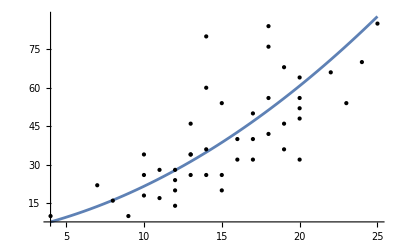

```mathematica
Plot[nlm[x], {x, 4, 25}, Epilog -> Point[dataCar], PlotRange -> All]
```

Let’s compare the two models:

```mathematica
#->{lm[#],nlm[#]}&/@ {"RSquared","AIC"}
```

{RSquared→{0.651079,0.667331},AIC→{419.198,418.866}}

```mathematica
LLMSynthesize["When analyzing linear model fits, are larger or smaller values of AICs (Akaike's Information Criterion) better?"]
```

When analyzing linear model fits, smaller values of AIC (Akaike's Information Criterion) are considered better. AIC is a statistical measure used for model selection and comparison. It aims to balance the goodness-of-fit of a model with its complexity. 

The AIC is calculated as AIC = -2 * log-likelihood + 2 * number of parameters. It penalizes models with more parameters, favoring simpler models that still provide a good fit to the data. 

Hence, when comparing different models, the model with the smaller AIC is preferred as it indicates a better balance between model fit and complexity.

```mathematica
LLMSynthesize["Based on the physics of a breaking car, would it be more realistic to assume a linear relationship between speed and stopping distance or would a quadratic relationship be better?"]
```

A quadratic relationship between speed and stopping distance is typically more realistic based on the physics of a braking car. According to the laws of physics, the stopping distance (d) of a car while it brakes depends on the initial speed (v) and other factors such as the coefficient of friction between the tires and the road, the condition of the road surface, the vehicle's braking system effectiveness, and the reaction time of the driver.

When a car brakes, the process involves multiple forces, including the force of friction acting in the opposite direction to the motion of the car. The force of friction is proportional to the normal force and the coefficient of friction. The normal force, in turn, is dependent on the weight of the vehicle, which remains constant.

Mathematically, the force of friction can be expressed as F = μN, where μ represents the coefficient of friction and N represents the normal force. In the case of a braking car, the force of friction serves to decelerate the vehicle, leading to a change in velocity.

Considering a linear relationship between speed and stopping distance would assume that the force of friction remains constant regardless of the speed. However, in reality, as the speed increases, the force of friction needed to bring the vehicle to a stop increases as well. This is because as the speed increases, the time available to decelerate before coming to a stop decreases, requiring a greater force of friction to achieve the same deceleration.

Hence, a quadratic relationship fits better with the physics of a braking car. As speed increases, the stopping distance will increase exponentially due to the interplay of factors such as the coefficient of friction, weight, and reaction time.